# Homework 8

Name: Eslam Muhammed Ahmed Zenhom

ID: 201700788

## Problem 1: Fig 6.10:

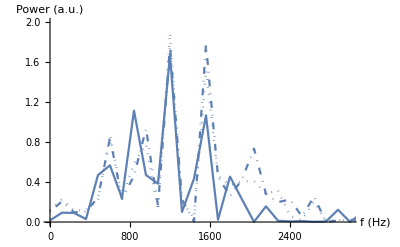

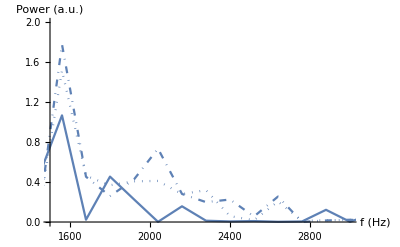

```mathematica
ClearAll["Global`*"];
speed = 300.0; x0=0.45; kk = 1000;  dx = 1/100; iMax = 1/dx; nMax=1000; dt = dx/(4*speed); rr =(speed dt)/dx;
(*for epsilon =0.00001*)
ϵ=(0.00001);  M=1/dx;
y[i_]:= Exp[-kk (i dx-x0)^2]
ymat = ConstantArray[0,{nMax,iMax+1}];
ymat[[1]] = Table[y[i],{i,1,Length[ymat[[1]]]}];
ymat[[2]] = ymat[[1]];

Do[Do[ymat[[All,1]]=0;
ymat[[n,i]] = (2(1 - rr^2)-6*ϵ*(rr^2)*(M^2))*ymat[[n-1,i]]-ymat[[n-2,i]]+rr^2*(1+4*ϵ*M^2)* (ymat[[n-1,i+1]]+ymat[[n-1,i-1]])-ϵ*(rr^2)*(M^2)*(ymat[[n-1,i+2]]+ymat[[n-1,i-2]]);ymat[[All,iMax+1]]=0;,{i,3,iMax-1}],{n,3,nMax}]

ft=Abs[Fourier[ymat[[All,iMax-5]]]]^2;
datf=Table[{(k-1)/(nMax dt), ft[[k]]},{k,1,nMax/2-1}];pl1=ListPlot[datf,PlotRange->{{0,3000},{0,2}},Joined->True,AxesLabel->{"f (Hz)","Power (a.u.)"},PlotStyle->{Dotted}];
pl11=ListPlot[datf,PlotRange->{{1500,3000},{0,2}},Joined->True,AxesLabel->{"f (Hz)","Power (a.u.)"},PlotStyle->{Dotted}];

(*for epsilon =2*0.00001*)

ϵ2=(2*0.00001);  
y2[i_]:= Exp[-kk (i dx-x0)^2]
ymat2 = ConstantArray[0,{nMax,iMax+1}];
ymat2[[1]] = Table[y[i],{i,1,Length[ymat[[1]]]}];
ymat2[[2]] = ymat2[[1]];

Do[Do[ymat2[[All,1]]=0;
ymat2[[n,i]] = (2(1 - rr^2)-6*ϵ2*(rr^2)*(M^2))*ymat2[[n-1,i]]-ymat2[[n-2,i]]+rr^2*(1+4*ϵ2*M^2)* (ymat2[[n-1,i+1]]+ymat2[[n-1,i-1]])-ϵ2*(rr^2)*(M^2)*(ymat2[[n-1,i+2]]+ymat2[[n-1,i-2]]);ymat2[[All,iMax+1]]=0,{i,3,iMax-1}],{n,3,nMax}]

ft2=Abs[Fourier[ymat2[[All,iMax-5]]]]^2;
datf2=Table[{(k-1)/(nMax dt), ft2[[k]]},{k,1,nMax/2-1}];pl2=ListPlot[datf2,PlotRange->{{0,3000},{0,2}},Joined->True,AxesLabel->{"f (Hz)","Power (a.u.)"},PlotStyle->{DotDashed}];
pl22=ListPlot[datf2,PlotRange->{{1500,3000},{0,2}},Joined->True,AxesLabel->{"f (Hz)","Power (a.u.)"},PlotStyle->{DotDashed}];

(*case for zero stiffness*)
ymat3 = ConstantArray[0,{nMax,iMax+1}];
ymat3[[1]] = Table[y[i],{i,1,Length[ymat3[[1]]]}];
ymat3[[2]] = ymat[[1]];

Do[Do[ymat3[[n,i]] = 2(1 - rr^2) ymat3[[n-1,i]]-ymat3[[n-2,i]]+rr^2 (ymat3[[n-1,i+1]]+ymat3[[n-1,i-1]]),{i,2,iMax}],{n,3,nMax}]
ft3=Abs[Fourier[ymat3[[All,iMax-5]]]]^2;
datf3=Table[{(k-1)/(nMax dt), ft3[[k]]},{k,1,nMax/2-1}];
pl3=ListPlot[datf3,PlotRange->{{0,3000},{0,2}},Joined->True,AxesLabel->{"f (Hz)","Power (a.u.)"}];
pl33=ListPlot[datf3,PlotRange->{{1500,3000},{0,2}},Joined->True,AxesLabel->{"f (Hz)","Power (a.u.)"}];

Show[pl1,pl2,pl3]
Show[pl11,pl22,pl33]
```

## Problem 2

(1)
 |  |  |  |

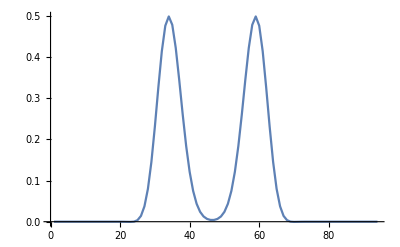

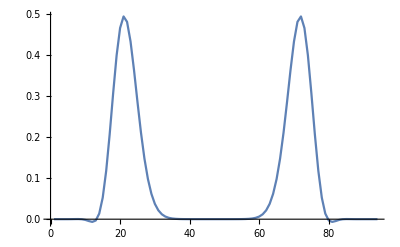

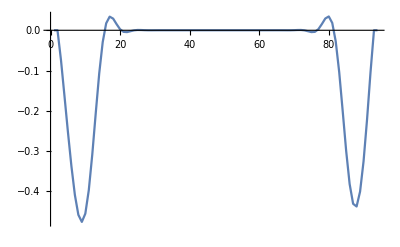

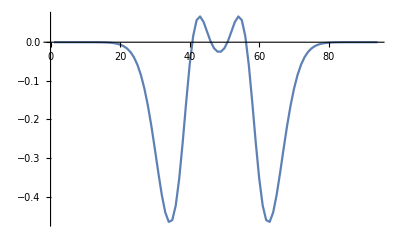

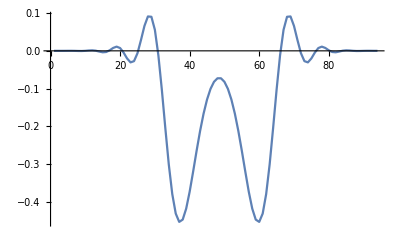

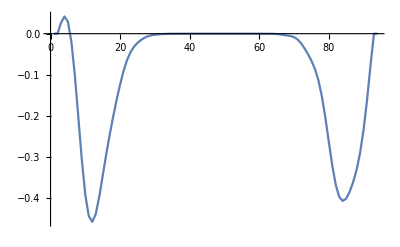

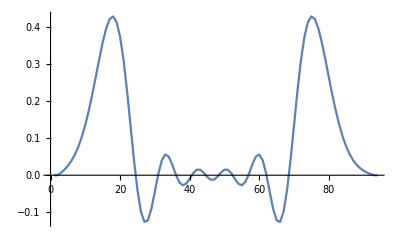

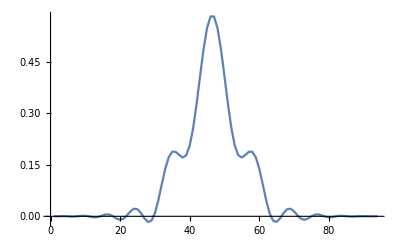

Table::nliter: Non-list iterator Joined→True at position 3 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

ListPlot::lpn: Table[ymat⟦FE`n$$68⟧,{FE`n$$68,1.,nMax},Joined→True,PlotRange→All] is not a list of numbers or pairs of numbers.

```mathematica
ClearAll["Global`*"]
speed = 330.0; x0=0.31; kk = 1000;  dx = 1/150; iMax = IntegerPart[0.62/dx]; nMax=1000; dt = dx/(4*speed); rr =(speed dt)/dx;
ϵ=3.8*(10^(-5));  M=0.62/dx;
b=0.5;
y[i_]:= Exp[-kk (i dx-x0)^2]
ymat = ConstantArray[0,{nMax,iMax+1}];
ymat[[1]] = Table[y[i],{i,1,Length[ymat[[1]]]}];
ymat[[2]] = ymat[[1]];
ymat[[1,1]]=0;
ymat[[2,1]]=0;
ymat[[1,iMax+1]]=0;
ymat[[2,iMax+1]]=0;
Do[Do[ymat[[n,i]] = ((2(1 - rr^2)-(6*ϵ*(rr^2)*(M^2)))/(1+b*dt))*ymat[[n-1,i]]+((-1+b*dt)/(1+b*dt))*ymat[[n-2,i]]+((rr^2*(1+4*ϵ*M^2))/(1+b*dt))* (ymat[[n-1,i+1]]+ymat[[n-1,i-1]])+((-ϵ*(rr^2)*(M^2))/(1+b*dt))*(ymat[[n-1,i+2]]+ymat[[n-1,i-2]]),{i,3,iMax-1}],{n,3,nMax}]
ymat//MatrixForm
signal = Table[{n dt,ymat[[n,6]]},{n,1,nMax}];
ListPlot[signal,Joined->True,PlotRange->All];
Manipulate[ListPlot[Table[ymat[[n]],{n,1,nMax},Joined->True,PlotRange->All]],{n,1,nMax}]
(* Don't know why manipulate don't work. but I have plotted manualy differnt instances of time*)

ListPlot[ymat[[50]],Joined->True,PlotRange->All]
ListPlot[ymat[[100]],Joined->True,PlotRange->All]
ListPlot[ymat[[200]],Joined->True,PlotRange->All]
ListPlot[ymat[[300]],Joined->True,PlotRange->All]
ListPlot[ymat[[400]],Joined->True,PlotRange->All]
ListPlot[ymat[[500]],Joined->True,PlotRange->All]
ListPlot[ymat[[600]],Joined->True,PlotRange->All]
ListPlot[ymat[[700]],Joined->True,PlotRange->All]
ListPlot[ymat[[800]],Joined->True,PlotRange->All]
ListPlot[ymat[[900]],Joined->True,PlotRange->All]
ListPlot[ymat[[950]],Joined->True,PlotRange->All]
ListPlot[ymat[[960]],Joined->True,PlotRange->All]
ListPlot[ymat[[970]],Joined->True,PlotRange->All]
ListPlot[ymat[[990]],Joined->True,PlotRange->All]
ListPlot[ymat[[999]],Joined->True,PlotRange->All]
```